```mathematica
ClearAll["Global`*"]
```

# Analytical expressions for stationary probability distribution and stochastic potential of autoc.-FB

How does the stationary probability of a Fokker-Plank associated with the autocatalytic feedback loop change if I change the cooperativity index of the Hill function? Vedi Quad P 2.4, 19/3/25

## Analytical expression for the stochastic potential

Which is basically the exponent of the probability function but - nicely - does not have normalization constants in the way.

#### Potential depending on changing Hill’s exponent

This is for

```mathematica
(2/σ^2 )*∫(k+a*(x^n)/(1+x^n)-x)ⅆx
```

(2 (k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n)))/σ^2

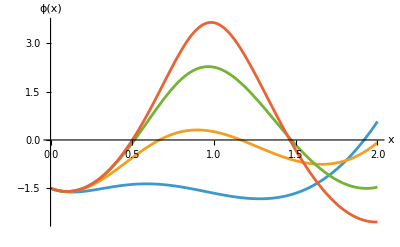

```mathematica
σ=0.05;
k=0.1;
a=1.9;
a1={1.9,1.85,1.8,1.7};
n={2,3,5,8};
Plot[{-(k x-x^2/2+(a x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ]},{x,0,2},AxesLabel->{Style["x",FontSize->{16}],Style["ϕ(x)",FontSize->{16}]}]
```

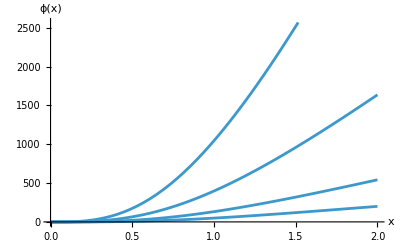

```mathematica
σ=0.05;
k=0.1;
a=1.9;
a1={1.9,1.85,1.8,1.7};
n={2,3,5,8};
Plot[{(2*k x-x^2+(2*a *(n^2 )* x^(1+n[[1]]) Hypergeometric2F1[1,(3*n[[1]]-1)/n[[1]],1+(4*n[[1]]-1)/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ]},{x,0,2},AxesLabel->{Style["x",FontSize->{16}],Style["ϕ(x)",FontSize->{16}]}]
```

## Expression for the probability function

Normalization constants

```mathematica
N1 =NIntegrate[Exp[-(-(k x-x^2/2+(a1[[1]] *x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ])],{x,0,3}];
N2 = NIntegrate[Exp[-(-(k x-x^2/2+(a1[[2]]*x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ])],{x,0,3}];
N3 = NIntegrate[Exp[-(-(k x-x^2/2+(a1[[3]]*x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ])],{x,0,3}];
N4 = NIntegrate[Exp[-(-(k x-x^2/2+(a1[[4]]*x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ])],{x,0,3}];
```

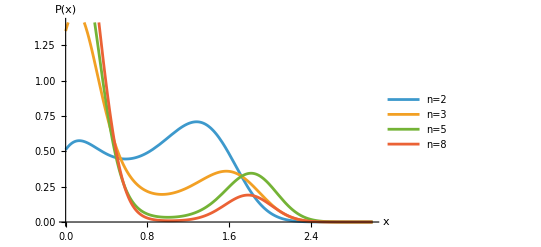

```mathematica
Plot[{(1/N1)*Exp[-(-(k x-x^2/2+(a1[[1]] x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ])],(1/N2)*Exp[-(-(k x-x^2/2+(a1[[2]] x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ])],(1/N3)*Exp[-(-(k x-x^2/2+(a1[[3]] x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ])],(1/N4)*Exp[-(-(k x-x^2/2+(a1[[4]] x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ])]},{x,0,3},PlotLegends->{"n=2","n=3","n=5","n=8"},AxesLabel->{Style["x",FontSize->{16}],Style["P(x)",FontSize->{16}]}]
```

```mathematica
Plot[Exp[((k x-x^2/2+(a1[[2]] x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ-0.5 Log[σ])],{x,0,3}]
```

#### Nice plots

```mathematica
Clear[σ,k,a,n]
```

```mathematica
k=0.1;
σ=0.02;
a={1.85,1.8,1.75,1.7}; (* very close to critical value *)
n={2,3,5,8};
ϕ[a_,n_][x_]:=-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ]
P[n_,a_][x_]:=Exp[-(-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ])]
norma[n_,a_][x_]:=NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ])],{x,0,10}];
norm1={norma[n[[1]],a[[1]]][x], norma[n[[2]],a[[2]]][x], norma[n[[3]],a[[3]]][x], norma[n[[4]],a[[4]]][x]};
```

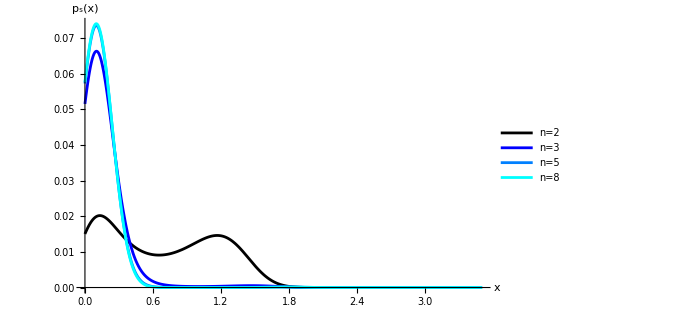

```mathematica
p1=Plot[{σ*P[n[[1]],a[[1]]][x]/norm1[[1]],σ*P[n[[2]],a[[2]]][x]/norm1[[2]],σ*P[n[[3]],a[[3]]][x]/norm1[[3]],σ*P[n[[4]],a[[4]]][x]/norm1[[4]]},{x,0,3.5},PlotStyle->{{Black,Line},{Line,RGBColor[0,0,1]},{Line,RGBColor[0,0.5,1]},{Line,RGBColor[0,1,1]}},AxesLabel->{Style["x",FontSize->16],Style["p_s(x)",FontSize->16]},PlotRange->All,PlotLegends->Placed[LineLegend[{"n=2","n=3","n=5","n=8"},LabelStyle->{GrayLevel[0.2],15},LegendLayout->{"Row",2}],{0.65,0.75}]]
```

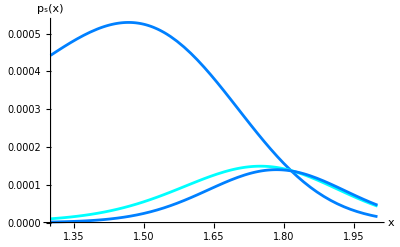

```mathematica
p1=Plot[{σ*P[n[[2]],a[[2]]][x]/norm1[[2]],σ*P[n[[3]],a[[3]]][x]/norm1[[3]],σ*P[n[[4]],a[[4]]][x]/norm1[[4]]},{x,1.3,2},PlotStyle->{{Line,RGBColor[0,0.5,1]},{Line,RGBColor[0,1,1]}},AxesLabel->{Style["x",FontSize->16],Style["p_s(x)",FontSize->16]},PlotRange->All]
```

```mathematica
norm1
```

{1.77381×10^6,4.60836×10^7,3.03171×10^9,2.42713×10^10}

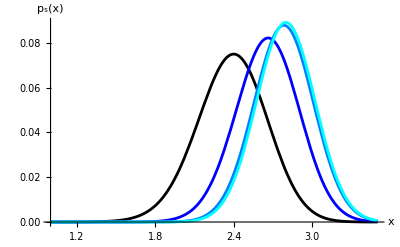

```mathematica
aUp=2.7; (* far from critical value, on upper branch *)
norm2=Flatten[{norma[n[[1]],aUp][x], norma[n[[2]],aUp][x], norma[n[[3]],aUp][x], norma[n[[4]],aUp][x]}]
p2=Plot[{σ*P[n[[1]],aUp][x]/norm2[[1]],σ*P[n[[2]],aUp][x]/norm2[[2]],σ*P[n[[3]],aUp][x]/norm2[[3]],σ*P[n[[4]],aUp][x]/norm2[[4]]},{x,1,3.5},AxesLabel->{Style["x",FontSize->16],Style["p_s(x)",FontSize->16]},PlotStyle->{{Black,Line},{Line,RGBColor[0,0,1]},{Line,RGBColor[0,0.5,1]},{Line,RGBColor[0,1,1]}}]
```

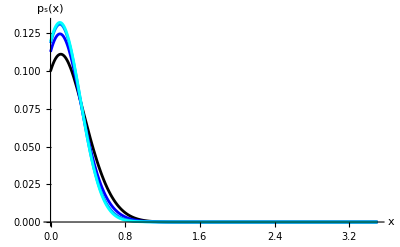

```mathematica
aLow=0.8;
norm3={norma[n[[1]],aLow][x], norma[n[[2]],aLow][x], norma[n[[3]],aLow][x], norma[n[[4]],aLow][x]};
p3=Plot[{σ*P[n[[1]],aLow][x]/norm3[[1]],σ*P[n[[2]],aLow][x]/norm3[[2]],σ*P[n[[3]],aLow][x]/norm3[[3]],σ*P[n[[4]],aLow][x]/norm3[[4]]},{x,0,3.5},AxesLabel->{Style["x",FontSize->16],Style["p_s(x)",FontSize->16]},PlotStyle->{{Black,Line},{Line,RGBColor[0,0,1]},{Line,RGBColor[0,0.5,1]},{Line,RGBColor[0,1,1]}},PlotRange->All]
```

#### Integrating the p(x) in some nice domain

```mathematica
∫_0^0.5 (Exp[-(-(kappa x-x^2/2+(1.9* x^(1+enne) Hypergeometric2F1[1,(1+enne)/enne,1+(1+enne)/enne,-x^enne])/(1+enne))/sigma+0.5 Log[sigma])/.{enne->2,kappa->0.1,sigma->0.05}])ⅆx
```

∫_0^0.5 ⅇ^(1.49787+20. (0.1 x-x^2/2+1.9 (x-ArcTan[x])))ⅆx

```mathematica
Solve[∫_0^0.5 (ⅇ^((0.1 x-x^2/2+1.9 (x-ArcTan[x]))/sigma))/sigma^0.5 ⅆx]
```

Solve::naqs: ∫_0^0.5 (ⅇ^((0.1 x-x^2/2+1.9 (x+Times[«2»]))/sigma))/sigma^0.5 ⅆx is not a quantified system of equations and inequalities.

Solve[∫_0^0.5 (ⅇ^((0.1 x-x^2/2+1.9 (x-ArcTan[x]))/sigma))/sigma^0.5 ⅆx]

```mathematica
(2-0.15)/(12*0.05)+0.5+Log[0.05]
```

#### Can ensure bistability?

```mathematica
a1=1.9;
k=0.1;
σ=0.05;
n={2,3,5,8};
```

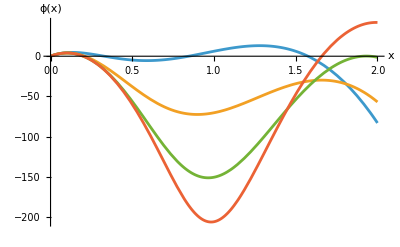

```mathematica
Plot[{(2 (k x-x^2/2+(a1* x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]])))/σ^2,(2 (k x-x^2/2+(a1*x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]])))/σ^2,(2 (k x-x^2/2+(a1* x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]])))/σ^2,(2 (k x-x^2/2+(a1*x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-(x^n)[[4]]])/(1+n[[4]])))/σ^2},{x,0,2},AxesLabel->{Style["x",FontSize->{16}],Style["ϕ(x)",FontSize->{16}]}]
```

```mathematica
Plot[Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]],{x,0,2}]
```

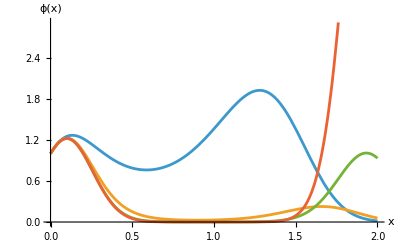

```mathematica
Plot[{Exp[(2 (k x-x^2/2+(a1* x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]])))/σ],Exp[(2 (k x-x^2/2+(a1*x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]])))/σ],Exp[(2 (k x-x^2/2+(a1* x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]])))/σ],Exp[(2 (k x-x^2/2+(a1*x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-(x^n)[[4]]])/(1+n[[4]])))/σ]},{x,0,2},AxesLabel->{Style["x",FontSize->{16}],Style["ϕ(x)",FontSize->{16}]}]
```

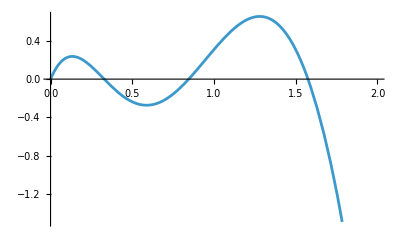

```mathematica
Plot[(2 (k x-x^2/2+(a1* x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]])))/σ,{x,0,2}]
```

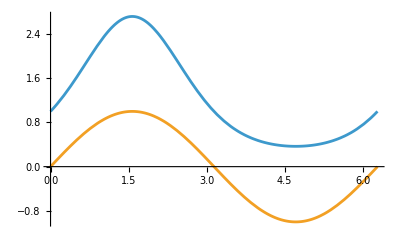

```mathematica
Plot[{Exp[Sin[x]],Sin[x]},{x,0,2Pi}]
```

## Rifaccio i calcoli, per scrupolo

```mathematica
(2/λ^2 )*∫(r+a*(x^n)/(1+x^n)-x)ⅆx
```

(2 (r x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n)))/λ^2